```mathematica
(*
written by S. Gonzalez
last updated May 20 2024
*)



(*import the data*)
init="3";
ydim = "2.301";
rad = 0.74;
ylength=10.5;

topDir = NotebookDirectory[]<>"k1len10500y/init_" <> init <>"/yresults_" <> ydim <> "/";


(*make the spline and tilings*)

CellPropsIn = Import[topDir<>"CellPropsOut.dat","CSV"];

co2co = CellPropsIn⟦1,1⟧;
θ = CellPropsIn⟦1,2⟧;
c=CellPropsIn⟦1,3⟧;
w=CellPropsIn⟦1,4⟧;
χc = CellPropsIn⟦1,5⟧;
χw = CellPropsIn⟦1,6⟧;
dHalf =( c-co2co)/2;

sd=7;

rotc = {{Cos[χc],0,-Sin[χc]},{0,1,0},{Sin[χc],0,Cos[χc]}};
trc = c/2{1 + Cos[χc],0,Sin[χc]};

rotw = {{1,0,0},{0,Cos[χw],-Sin[χw]},{0,Sin[χw],Cos[χw]}};
trw = w/2{0,1 + Cos[χw],Sin[χw]};

rot = {1,1,1};


BezIn = Import[topDir<>"BezierOut.dat","CSV"];
BezList = Table[Table[Table[rot⟦Mod[i-1,3]+1⟧*BezIn⟦k,i⟧,{i,3*(j-1)+1,3*(j-1)+3}],{j,1,Length[BezIn⟦k⟧]/3}],{k,1,Length[BezIn]}];

BezInCourse = Import[topDir<>"BezierOutCourse.dat","CSV"];
BezListCourse = Table[Table[Table[rot⟦Mod[i-1,3]+1⟧*BezInCourse⟦k,i⟧,{i,3*(j-1)+1,3*(j-1)+3}],{j,1,Length[BezInCourse⟦k⟧]/3}],{k,1,Length[BezInCourse]}];
BezListCourse2 = Table[Table[Table[rot⟦Mod[i-1,3]+1⟧*BezInCourse⟦k,i⟧,{i,3*(j-1)+1,3*(j-1)+3}]-{c,0,0},{j,1,Length[BezInCourse⟦k⟧]/3}],{k,1,Length[BezInCourse]}];

BezInWale = Import[topDir<>"BezierOutWale.dat","CSV"];
BezListWale = Table[Table[Table[rot⟦Mod[i-1,3]+1⟧*BezInWale⟦k,i⟧,{i,3*(j-1)+1,3*(j-1)+3}],{j,1,Length[BezInWale⟦k⟧]/3}],{k,1,Length[BezInWale]}];
BezListWale2 = Table[Table[Table[rot⟦Mod[i-1,3]+1⟧*BezInWale⟦k,i⟧,{i,3*(j-1)+1,3*(j-1)+3}]-{0,w,0},{j,1,Length[BezInWale⟦k⟧]/3}],{k,1,Length[BezInWale]}];

tvalues = Range[0.0,0.9,0.1];

p1=BezierFunction[BezList[[4]]];
part1 = Table[p1[tvalues[[i]]],{i,1,Length@tvalues}];
part1shifted = Table[{part1[[i,1]], (part1[[i,2]]-w), part1[[i,3]]},{i,1,Length@part1}];
part1shifted = Reverse[part1shifted];


p2=BezierFunction[BezListWale2[[2]]];
part2 = Table[p2[tvalues[[i]]],{i,1,Length@tvalues}];
part2=Reverse[part2];



p3=BezierFunction[BezList[[2]]];
part3 = Table[p3[tvalues[[i]]],{i,1,Length@tvalues}];
part3=Reverse[part3];



p4=BezierFunction[BezList[[5]]];
part4 = Table[p4[tvalues[[i]]],{i,1,Length@tvalues}];
part4=Reverse[part4];



p5=BezierFunction[BezList[[1]]];
part5 = Table[p5[tvalues[[i]]],{i,1,Length@tvalues}];
part5=Reverse[part5];



p6=BezierFunction[BezListWale2[[1]]];
part6 = Table[p6[tvalues[[i]]],{i,1,Length@tvalues}];
part6=Reverse[part6];



p7=BezierFunction[BezList[[3]]];
part7 = Table[p7[tvalues[[i]]],{i,1,Length@tvalues}];
part7shifted = Table[{part7[[i,1]], (part7[[i,2]]-w), part7[[i,3]]},{i,1,Length@part7}];
part7shifted=Reverse[part7shifted];



p8=BezierFunction[BezListCourse[[1]]];
part8 = Table[p8[tvalues[[i]]],{i,1,Length@tvalues}];
part8shifted = Table[{(part8[[i,1]]), (part8[[i,2]]-w), part8[[i,3]]},{i,1,Length@part8}];
part8shifted=Reverse[part8shifted];

Length@part8shifted

left = Table[part8shifted[[i]]-{c,0,0},{i,1,5}];

all = Join[left,part1shifted,part2, part3, part4, part5, part6, part7shifted, part8shifted[[5;;]]];
homie=all;

zall = Table[all[[i,3]],{i, 1, Length@all}];
Min@zall
Max@zall

ListPointPlot3D[all]

allleft = Table[{all[[i,1]]+c, all[[i,2]],all[[i,3]]},{i,1,Length@all}];
allright = Table[{all[[i,1]]-c, all[[i,2]],all[[i,3]]},{i,1,Length@all}];
allup= Table[{all[[i,1]], all[[i,2]]+w,all[[i,3]]},{i,1,Length@all}];
alldown= Table[{all[[i,1]], all[[i,2]]-w,all[[i,3]]},{i,1,Length@all}];
allup2= Table[{all[[i,1]], all[[i,2]]+2*w,all[[i,3]]},{i,1,Length@all}];
alldown2= Table[{all[[i,1]], all[[i,2]]-2*w,all[[i,3]]},{i,1,Length@all}];

allup2left= Table[{all[[i,1]]-c, all[[i,2]]+2*w,all[[i,3]]},{i,1,Length@all}];
alldown2right= Table[{all[[i,1]]+c, all[[i,2]]-2*w,all[[i,3]]},{i,1,Length@all}];

(*NEED TO EXCLUDE POINTS FROM LEFT AND RIGHT OR ELSE WE ARE GOING TO GET OVERLAPS AT THE END OF THE STITCH*)
ListPointPlot3D[allright[[8;;72]]]

others=Join[allleft[[8;;70]], allright[[8;;72]],allup,alldown, allup2, alldown2, allup2left, alldown2right];
ListPointPlot3D[others]
```

Import::nffil: File /Users/sgonzalez49/GaTech Dropbox/Sarah Gonzalez/Desktopcopy/mikewhy/stockjamsweeps/simulationdata/contactvolumedata/k1len10500y/init_3/yresults_2.301/CellPropsOut.dat not found during Import.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,3⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,4⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,5⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,6⟧ is longer than depth of object.

Import::nffil: File /Users/sgonzalez49/GaTech Dropbox/Sarah Gonzalez/Desktopcopy/mikewhy/stockjamsweeps/simulationdata/contactvolumedata/k1len10500y/init_3/yresults_2.301/BezierOut.dat not found during Import.

Import::nffil: File /Users/sgonzalez49/GaTech Dropbox/Sarah Gonzalez/Desktopcopy/mikewhy/stockjamsweeps/simulationdata/contactvolumedata/k1len10500y/init_3/yresults_2.301/BezierOutCourse.dat not found during Import.

Import::nffil: File /Users/sgonzalez49/GaTech Dropbox/Sarah Gonzalez/Desktopcopy/mikewhy/stockjamsweeps/simulationdata/contactvolumedata/k1len10500y/init_3/yresults_2.301/BezierOutWale.dat not found during Import.

Part::partw: Part 4 of {} does not exist.

BezierFunction::invcpts: {}⟦4⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 2 of BezierFunction[{}⟦4⟧][0.] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦4⟧][0.] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦4⟧][0.1] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

BezierFunction::invcpts: {}⟦2⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 2 of {} does not exist.

BezierFunction::invcpts: {}⟦2⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 5 of {} does not exist.

BezierFunction::invcpts: {}⟦5⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 1 of {} does not exist.

BezierFunction::invcpts: {}⟦1⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 1 of {} does not exist.

BezierFunction::invcpts: {}⟦1⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 3 of {} does not exist.

BezierFunction::invcpts: {}⟦3⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 2 of BezierFunction[{}⟦3⟧][0.] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦3⟧][0.] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦3⟧][0.1] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

BezierFunction::invcpts: {}⟦1⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 2 of BezierFunction[{}⟦1⟧][0.] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦1⟧][0.] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦1⟧][0.1] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

10

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.8] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.7] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.8] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.8] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.8] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.8] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.8] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.8] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.8] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.8] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.8] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦2⟧][0.9] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.8] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

```mathematica
tvalues = Range[0.0,0.999,0.001];

p1=BezierFunction[BezList[[4]]];
part1 = Table[p1[tvalues[[i]]],{i,1,Length@tvalues}];
part1shifted = Table[{part1[[i,1]], (part1[[i,2]]-w), part1[[i,3]]},{i,1,Length@part1}];
part1shifted = Reverse[part1shifted];


p2=BezierFunction[BezListWale2[[2]]];
part2 = Table[p2[tvalues[[i]]],{i,1,Length@tvalues}];
part2=Reverse[part2];



p3=BezierFunction[BezList[[2]]];
part3 = Table[p3[tvalues[[i]]],{i,1,Length@tvalues}];
part3=Reverse[part3];



p4=BezierFunction[BezList[[5]]];
part4 = Table[p4[tvalues[[i]]],{i,1,Length@tvalues}];
part4=Reverse[part4];



p5=BezierFunction[BezList[[1]]];
part5 = Table[p5[tvalues[[i]]],{i,1,Length@tvalues}];
part5=Reverse[part5];



p6=BezierFunction[BezListWale2[[1]]];
part6 = Table[p6[tvalues[[i]]],{i,1,Length@tvalues}];
part6=Reverse[part6];



p7=BezierFunction[BezList[[3]]];
part7 = Table[p7[tvalues[[i]]],{i,1,Length@tvalues}];
part7shifted = Table[{part7[[i,1]], (part7[[i,2]]-w), part7[[i,3]]},{i,1,Length@part7}];
part7shifted=Reverse[part7shifted];



p8=BezierFunction[BezListCourse[[1]]];
part8 = Table[p8[tvalues[[i]]],{i,1,Length@tvalues}];
part8shifted = Table[{(part8[[i,1]]), (part8[[i,2]]-w), part8[[i,3]]},{i,1,Length@part8}];
part8shifted=Reverse[part8shifted];

left = Table[part8shifted[[i]]-{c,0,0},{i,1,500}];

all = Join[part8shifted[[500;;]],part1shifted,part2, part3, part4, part5, part6, part7shifted, left];

all2d = Table[{all[[i,1]], all[[i,2]]},{i,1,Length@all}];
left2d=Table[{left[[i,1]], left[[i,2]]},{i,1,Length@left}];
part1shifted2d=Table[{part1shifted[[i,1]], part1shifted[[i,2]]},{i,1,Length@part1shifted}];
Show[ListPlot[all2d], ListPlot[part1shifted2d, PlotStyle->Yellow], ListPlot[left2d, PlotStyle->Green]]

finish=Length@all2d - 1
normalvector=Table[{(all2d[[i+1,2]]-all2d[[i-1,2]]),-1*(all2d[[i+1,1]]-all2d[[i-1,1]])},{i,2,finish}];
normalunit=Table[{(normalvector[[i,1]]/Sqrt[(normalvector[[i,1]]^2 + normalvector[[i,2]]^2)]),(normalvector[[i,2]]/Sqrt[(normalvector[[i,1]]^2 + normalvector[[i,2]]^2)])}, {i,1,Length@normalvector}]

offset=0.74

up = Table[{(all2d[[i+1,1]]+offset*normalunit[[i,1]]),(all2d[[i+1,2]]+offset*normalunit[[i,2]]) ,1}, {i,1, Length@normalunit}];

down = Table[{(all2d[[i+1,1]]-offset*normalunit[[i,1]]),(all2d[[i+1,2]]-offset*normalunit[[i,2]]) ,1}, {i,1, Length@normalunit}];

Length@down

Show[ListPointPlot3D[up, PlotStyle->Green],ListPointPlot3D[down, PlotStyle->Magenta],ListPointPlot3D[down[[7990;;]], PlotStyle->Blue], PlotRange->All]
```

Part::partw: Part 4 of {} does not exist.

BezierFunction::invcpts: {}⟦4⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 2 of BezierFunction[{}⟦4⟧][0.] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦4⟧][0.] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦4⟧][0.001] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

BezierFunction::invcpts: {}⟦2⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 2 of {} does not exist.

BezierFunction::invcpts: {}⟦2⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 5 of {} does not exist.

BezierFunction::invcpts: {}⟦5⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 1 of {} does not exist.

BezierFunction::invcpts: {}⟦1⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 1 of {} does not exist.

BezierFunction::invcpts: {}⟦1⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 3 of {} does not exist.

BezierFunction::invcpts: {}⟦3⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 2 of BezierFunction[{}⟦3⟧][0.] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦3⟧][0.] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦3⟧][0.001] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

BezierFunction::invcpts: {}⟦1⟧ should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partw: Part 2 of BezierFunction[{}⟦1⟧][0.] does not exist.

Part::partw: Part 3 of BezierFunction[{}⟦1⟧][0.] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦1⟧][0.001] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.999] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.998] does not exist.

Part::partw: Part 2 of BezierFunction[{}⟦2⟧][0.997] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

8000

```mathematica
(*make grid*)
homiex= Table[homie[[i,1]],{i,1,Length@homie}];
homiey= Table[homie[[i,2]],{i,1,Length@homie}];
homiez= Table[homie[[i,3]],{i,1,Length@homie}];

voxelbounds = {
Min[homiex],
Max[homiex],
Min[homiey],
Max[homiey],
Min[homiez],
Max[homiez]
};

t= 0.045;

xrange = Range[((Round[voxelbounds[[1]],t]-rad)-10*t),((Round[voxelbounds[[2]],t]+rad)+10*t), t];
yrange = Range[((Round[voxelbounds[[3]],t]-rad)-10*t),((Round[voxelbounds[[4]],t]+rad)+10*t), t];
zrange = Range[((Round[voxelbounds[[5]],t]-rad)-10*t),((Round[voxelbounds[[6]],t]+rad)+10*t), t];

points=Table[Table[Table[{xrange[[i]],yrange[[j]],zrange[[k]]},{k,1,Length@zrange}],{j,1,Length@yrange}],{i,1,Length@xrange}];
points =Flatten[points,2];
points[[1]];
points[[2]];
```

```mathematica
(*prep to find volume of stitch*)

distance[r1_, r2_]:={
Sqrt[((r1[[1]]-r2[[1]])^2 + (r1[[2]] - r2[[2]])^2 + (r1[[3]] - r2[[3]])^2)]
}

stitchpoints={};

For[i=1, i<Length@points, i++, For[j=1, j<Length@homie, j++, If[distance[points[[i]], homie[[j]]][[1]]<=rad,AppendTo[stitchpoints, points[[i]]];Break[]]]]

(*numerical volume including self contact and end caps*)
Length@stitchpoints*(t^3)
(*volume of cylinder formula*)
3.14*rad^2*ylength

Show[ListPointPlot3D[stitchpoints, PlotStyle->Magenta], ListPointPlot3D[homie], PlotRange->All]
```

21.8209

18.0544

-Graphics3D-

```mathematica
(*get rid of the end caps, total volume*)

cap = {};

leftpoint = homie[[80]];
rightpoint = homie[[1]];

leftfar = rightpoint-{c,0,0};
rightfar = leftpoint + {c,0,0};



For[i=1, i<Length@stitchpoints, i++, If[stitchpoints[[i,1]]>(rightpoint[[1]]-1.25*rad) && stitchpoints[[i,2]]<(rightpoint[[2]]+1.25*rad)  && distance[stitchpoints[[i]],rightpoint][[1]]>distance[stitchpoints[[i]], rightfar][[1]] ||stitchpoints[[i,1]]<0 && stitchpoints[[i,2]]<(leftfar[[2]]+1.25*rad)  && distance[stitchpoints[[i]],leftpoint][[1]]>distance[stitchpoints[[i]], leftfar][[1]], AppendTo[cap,stitchpoints[[i]]]]]

stitchpoints=DeleteElements[stitchpoints, cap];

uncompressedvolume=Length@stitchpoints*(t^3)
(*this already accounts for the self contact*)

Show[ListPointPlot3D[stitchpoints, PlotStyle->Magenta], ListPointPlot3D[homie], PlotRange->All]
```

20.095

-Graphics3D-

```mathematica
samerowcontacts = {};

row = Join[allleft[[8;;70]], allright[[8;;72]]];

For[i=1, i<Length@stitchpoints, i++, For[j=1, j<Length@row, j++, If[distance[stitchpoints[[i]], row[[j]]][[1]]<=rad, AppendTo[samerowcontacts, stitchpoints[[i]]];Break[]]]]

Length@samerowcontacts
samerowvolume=Length@samerowcontacts*(t^3)

samerowplot=Show[ListPointPlot3D[samerowcontacts, PlotStyle->Green], ListPointPlot3D[homie], PlotRange->All]
```

16586

1.5114

-Graphics3D-

```mathematica
samecolumncontactsup = {};
samecolumncontactsdown = {};

column = Join[allup, alldown];

For[i=1, i<Length@stitchpoints, i++, For[j=1, j<Length@allup, j++, If[distance[stitchpoints[[i]], allup[[j]]][[1]]<=rad, AppendTo[samecolumncontactsup, stitchpoints[[i]]];Break[]]]]

Length@samecolumncontactsup
samecolumnvolumeup=Length@samecolumncontactsup*(t^3)

For[i=1, i<Length@stitchpoints, i++, For[j=1, j<Length@alldown, j++, If[distance[stitchpoints[[i]], alldown[[j]]][[1]]<=rad, AppendTo[samecolumncontactsdown, stitchpoints[[i]]];Break[]]]]

Length@samecolumncontactsdown
samecolumnvolumedown=Length@samecolumncontactsdown*(t^3)

samecolumnplot=Show[ListPointPlot3D[samecolumncontactsup, PlotStyle->Blue],ListPointPlot3D[samecolumncontactsdown, PlotStyle->Cyan], ListPointPlot3D[homie], PlotRange->All]
```

52789

4.8104

52082

4.74597

-Graphics3D-

```mathematica
samesecondcolumncontacts = {};

secondcolumn = Join[allup2, alldown2, allup2left, alldown2right];

For[i=1, i<Length@stitchpoints, i++, For[j=1, j<Length@secondcolumn, j++, If[distance[stitchpoints[[i]], secondcolumn[[j]]][[1]]<=rad, AppendTo[samesecondcolumncontacts, stitchpoints[[i]]];Break[]]]]

Length@samesecondcolumncontacts
samesecondcolumnvolume=Length@samesecondcolumncontacts*(t^3)

samesecondcolumnplot=Show[ListPointPlot3D[samesecondcolumncontacts, PlotStyle->Orange], ListPointPlot3D[homie], PlotRange->All]
```

41061

3.74168

-Graphics3D-

```mathematica
overlaps = Join[samerowcontacts, samecolumncontactsup, samecolumncontactsdown, samesecondcolumncontacts]
overlapvolume=Length@overlaps*(t^3)

Compressedvolume = uncompressedvolume - (overlapvolume/2)

Show[ListPointPlot3D[overlaps, PlotStyle->Magenta], ListPointPlot3D[homie], PlotRange->All]
```

14.8095

12.6902

-Graphics3D-

```mathematica
(*calculate volume of stitch cell*)

zoverlaps = Table[overlaps[[i,3]],{i,1,Length@overlaps}];
zstitchpoints = Table[stitchpoints[[i,3]],{i,1,Length@overlaps}];

Min@zoverlaps
Max@zoverlaps

Min@zstitchpoints
Max@zstitchpoints

(*use stitchpoints because the stitchpoints go further in z than any of the compressed volumes*)

c;
w;
zwidth = Max@zstitchpoints - Min@zstitchpoints;
cellvolume = c*w*zwidth
```

-0.785

1.06

-1.1

1.195

16.248

```mathematica
(*ratio of yarn to unit cell volume*)
```

```mathematica
Compressedvolume/cellvolume
```

0.781036

```mathematica
(*self contact*)

(*Show[ListPointPlot3D[part1shifted], ListPointPlot3D[part7shifted], PlotRange->All]*)
homiel = part1shifted;

homielx= Table[homiel[[i,1]],{i,1,Length@homiel}];
homiely= Table[homiel[[i,2]],{i,1,Length@homiel}];
homielz= Table[homiel[[i,3]],{i,1,Length@homiel}];

voxelboundsl = {
Min[homielx],
Max[homielx],
Min[homiely],
Max[homiely],
Min[homielz],
Max[homielz]
};

xrangel = Range[(Round[voxelboundsl[[1]],t]-rad)-t,(Round[voxelboundsl[[2]],t]+rad)+t, t];
yrangel = Range[(Round[voxelboundsl[[3]],t]-rad)-t,(Round[voxelboundsl[[4]],t]+rad)+t, t];
zrangel = Range[(Round[voxelboundsl[[5]],t]-rad)-t,(Round[voxelboundsl[[6]],t]+rad)+t, t];

pointsl=Table[Table[Table[{xrangel[[i]],yrangel[[j]],zrangel[[k]]},{k,1,Length@zrangel}],{j,1,Length@yrangel}],{i,1,Length@xrangel}];
pointsl =Flatten[pointsl,2];
pointsl[[1]];
pointsl[[2]];

stitchpointsl={};

For[i=1, i<Length@pointsl, i++, For[j=1, j<Length@homiel, j++, If[distance[pointsl[[i]], homiel[[j]]][[1]]<=rad,AppendTo[stitchpointsl, pointsl[[i]]];Break[]]]]

Show[ListPointPlot3D[stitchpointsl, PlotStyle->Magenta], ListPointPlot3D[homiel], PlotRange->All]

uncompressedvolumel=Length@stitchpointsl*(t^3);

othersl = part7shifted;

overlapsl = {};

For[i=1, i<Length@stitchpointsl, i++, For[j=1, j<Length@othersl, j++, If[distance[stitchpointsl[[i]], othersl[[j]]][[1]]<=rad, AppendTo[overlapsl, stitchpointsl[[i]]];Break[]]]]

Length@overlapsl;
overlapvolumel=Length@overlapsl*(t^3)

Show[ListPointPlot3D[stitchpointsl, PlotStyle->Gray],ListPointPlot3D[overlapsl, PlotStyle->Magenta], ListPointPlot3D[homiel], PlotRange->All]
```

-Graphics3D-

0.767637

-Graphics3D-

```mathematica
Show[ListPointPlot3D[overlapsl, PlotStyle->Magenta, PlotStyle->PointSize[01]], ListPointPlot3D[homie], PlotRange->All, ViewPoint->Top]
```

-Graphics3D-

```mathematica
Show[samecolumnplot,samerowplot, samesecondcolumnplot,ListPointPlot3D[overlapsl, PlotStyle->Magenta], ViewPoint->{0,0,Infinity}, PointSize->1]
```

-Graphics3D-

```mathematica
rowalone=Show[ListPointPlot3D[samerowcontacts, PlotStyle->Directive[Magenta, PointSize-> 0.02, Opacity->0.1]], ListPointPlot3D[up,  PlotStyle->Directive[Black, PointSize-> 0.01]],  ListPointPlot3D[down,  PlotStyle->Directive[Black, PointSize-> 0.01]],  PlotRange->All, ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
rowalonetop=Show[ListPointPlot3D[samerowcontacts, PlotStyle->Directive[Green, PointSize-> 0.02, Opacity->0.1]], PlotRange->All, ViewPoint->{0,Infinity,0}]
rowaloneside=Show[ListPointPlot3D[samerowcontacts, PlotStyle->Directive[Green, PointSize-> 0.02, Opacity->0.1]],  PlotRange->All, ViewPoint->{Infinity,0,0}]
```

-Graphics3D-

-Graphics3D-

```mathematica
columnalone=Show[ListPointPlot3D[samecolumncontactsup, PlotStyle->Blue],ListPointPlot3D[samecolumncontactsdown, PlotStyle->Cyan], ListPointPlot3D[homie, PlotStyle->Orange], PlotRange->All, ViewPoint->{0.2,0.1,1}]
```

-Graphics3D-

```mathematica
columnalone=Show[ListPointPlot3D[samecolumncontactsup, PlotStyle->Directive[Darker[Blue,1/2], PointSize-> 0.02, Opacity->0.05]],ListPointPlot3D[samecolumncontactsdown, PlotStyle->Directive[Darker[Cyan,1/2], PointSize-> 0.02, Opacity->0.05]], ListPointPlot3D[up, PlotStyle->Directive[Black, PointSize-> 0.01]],  ListPointPlot3D[down, PlotStyle->Directive[Black, PointSize-> 0.01]], PlotRange->All, ViewPoint->{0,0,Infinity}]

columnalonetop=Show[ListPointPlot3D[samecolumncontactsup, PlotStyle->Directive[Blue, PointSize-> 0.02, Opacity->0.05]],ListPointPlot3D[samecolumncontactsdown, PlotStyle->Directive[Darker[Cyan,1/2], PointSize-> 0.02, Opacity->0.05]], PlotRange->All, ViewPoint->{0,Infinity,0}]

columnaloneside=Show[ListPointPlot3D[samecolumncontactsup, PlotStyle->Directive[Blue, PointSize-> 0.02, Opacity->0.05]],ListPointPlot3D[samecolumncontactsdown, PlotStyle->Directive[Darker[Cyan,1/2], PointSize-> 0.02, Opacity->0.05]], PlotRange->All, ViewPoint->{Infinity,0,0}]

columnaloneoblique=Show[ListPointPlot3D[samecolumncontactsup, PlotStyle->Directive[Blue, PointSize-> 0.02, Opacity->0.05]],ListPointPlot3D[samecolumncontactsdown, PlotStyle->Directive[Darker[Cyan,1/2], PointSize-> 0.02, Opacity->0.05]], PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
secondcolumnalone=Show[ListPointPlot3D[samesecondcolumncontacts, PlotStyle->Directive[Yellow, PointSize-> 0.02, Opacity->0.1]],ListPointPlot3D[up,PlotStyle->Directive[Black, PointSize-> 0.01]],  ListPointPlot3D[down,PlotStyle->Directive[Black, PointSize-> 0.01]],PlotRange->All, ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
selfalone=Show[ListPointPlot3D[overlapsl, PlotStyle->Directive[Green, PointSize-> 0.02, Opacity->0.1]], ListPointPlot3D[up, PlotStyle->Directive[Black, PointSize-> 0.01]],  ListPointPlot3D[down, PlotStyle->Directive[Black, PointSize-> 0.01]],PlotRange->All, ViewPoint->{0,0,Infinity}, FrameStyle->Directive[Black,FontFamily->"Helvetica",Thickness[0.1],Arrowheads[{0.0,0.05}], 30]]
```

-Graphics3D-

```mathematica
allplot=Show[columnalone,secondcolumnalone,rowalone,selfalone]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["10500row.png",rowalone]
Export["10500column.png",columnalone]
Export["10500secondcolumn.png",secondcolumnalone]
Export["10500self.png",selfalone]
Export["10500all.png",allplot]
```

12200row.png

12200column.png

12200secondcolumn.png

12200self.png

12200all.png

```mathematica
(*uncomment iff you are using this to calculate volume data over a strain sweep, which is not recommended due to speed. use the julia code instead.*)

(*listforexport=Import["voxeldata.csv", "CSV"];

(*total yarn volume if there were no self contacts*)
noselfuncompressedvolume = uncompressedvolume + overlapvolumel;

data= {ylength, c, w, zwidth, cellvolume, noselfuncompressedvolume, uncompressedvolume, Compressedvolume, Compressedvolume/cellvolume};

AppendTo[listforexport, data];

SetDirectory[NotebookDirectory[]];

Export["voxeldata.csv", listforexport]*)
```

voxeldata.csv

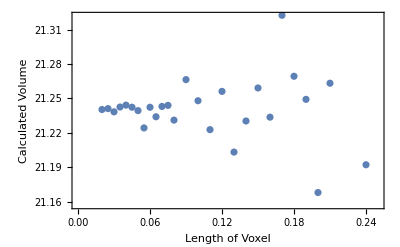

volumevsvoxel.pdf

```mathematica
(*voxel size study, done on length 12.2*)
tsize={
{21.375, 0.25},
{21.192192, 0.24},
{21.389586, 0.23},
{20.944616, 0.22},
{21.263255999999995, 0.21},
{21.168000000000006, 0.2},
{21.249182, 0.19},
{21.269303999999998, 0.18},
{21.322420000000008, 0.17},
{21.233664000000005, 0.16},
{21.259125, 0.15},
{21.230328000000007, 0.14},
{21.203247 , 0.13},
{21.256128 , 0.12},
{21.222794999999998 ,0.11},
{21.248000000000005 , 0.1},
{21.266388 , 0.09},
{21.231104000000002 ,0.08},
{21.2439375,0.075},
{21.243019000000007 , 0.07},
{21.234005000000003,0.065},
{21.242304 , 0.06},
{21.224292374999997,0.055},
{21.239375000000006 , 0.05},
{21.242330999999997, 0.045},
{21.244160000000004,0.04},
{21.242504500000006, 0.035},
{21.238308 ,0.03},
{21.241125000000004,0.025},
{21.240320000000004,0.02}
};

tsize=Reverse[tsize, 2];

voxelplot=Show[ListPlot[tsize], Frame->True, FrameLabel->{"l [mm]", "V_comp [mm^3]"},FrameStyle->Directive[Black,FontFamily->"Helvetica",(*Thickness[0.005],*)Arrowheads[{0.0,0.05}], 10]]
Export["volumevsvoxel.pdf",voxelplot]
```